## General identities

```mathematica
sG=-((a^2-1)(b^2-1))/(a+b)^2;
tG=(a^2-1)/(a (a+b));

sM=((a^2-1)(b^2-1))/(1+a b)^2;
tM=(1-a^2)/(1+a b);

lhs=1/((p-y)√((-y^2+α y-1)(y^2+β y+1)));
rhs=(2 √(a b))/((a+b) (b+p) (a p-1)) ((1-a p) EllipticK[sG]-(1+a b) EllipticPi[((-1+a^2) (b+p))/((a+b) (-1+a p)),sG]);

max=6;
lhsS=Series[p lhs,{p,∞,max}];
rhsS=Series[p rhs,{p,∞,max}];

Table[1/2 SeriesCoefficient[lhsS,m]==1/2 y^m/(√((-y^2+α y-1)(y^2+β y+1))),{m,0,max}]

VG[n_]:=Switch[n,0,(1+a b)/(a+b)EllipticK[sG],1,(1+a b)^2/(a (a+b)^2) EllipticPi[tG,sG],2,(1+a b)/(2 a b(a+b))EllipticE[sG]-(1+a b)^2/(2 a (a+b)^2)EllipticK[sG]+((1+a b)^2 (-a+b+a^2 b+3 a b^2))/(2 a^2 b (a+b)^3)EllipticPi[tG,sG],_,(1+2 (n-3))/(4+2 (n-3))((1+a b) (-1+b^2))/(a b (a+b)^2) VG[(n-3)]+(1+(n-3))/(2+(n-3))(1+a^2+a b-2 (1+a^2) b^2-3 a b^3)/(a b (a+b)^2) VG[(n-3)+1]+(3+2 (n-3))/(4+2 (n-3))(-a+b+a^2 b+3 a b^2)/(a b (a+b)) VG[(n-3)+2]] 

VM[n_]:=Switch[n,0,EllipticK[sM],1,EllipticPi[tM,sM],2,(tM EllipticE[sM]+(sM-tM)EllipticK[sM]+(2 sM tM+2 tM-tM^2-3 sM)EllipticPi[tM,sM])/(2 (sM-tM) (tM-1)),_,1/(2 ((n-3)+2) (sM-tM) (tM-1))(-(1+2 (n-3))sM VM[(n-3)]-2 (1+(n-3)) (sM tM+tM-3 sM) VM[1+(n-3)]+(2 (n-3)+3) (-tM^2+2 sM tM+2 tM-3 sM) VM[2+(n-3)])] 


IG[n_]:=(√(a b))/(1+a b)Sum[(-1)^(n+j+1)(a+b)^j b^(n-j)Binomial[n,j]VG[j],{j,0,max}]
IM[n_]:=(√(a b))/(1+a b)Sum[(-1)^(n+j+1)(a+b)^j b^(n-j)Binomial[n,j]VM[j],{j,0,max}]

Table[1/2 SeriesCoefficient[rhsS,m]==IG[m]//Simplify,{m,0,max}]
```

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

True

True

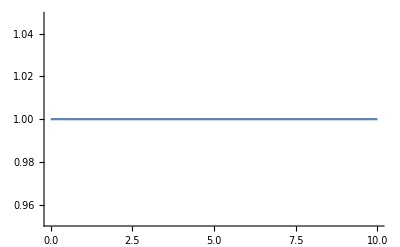

-Graphics-

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
tmp=Table[IM[m]//.Flatten[{{EllipticK[sM]->(1+a b)/(a+b)EllipticK[sG]}, {EllipticPi[tM,sM]->(1+a b)^2/(a(a+b)^2)EllipticPi[tG,sG]}, {EllipticPi[tM,sM]->(a+b)/(1+a b)EllipticE[sG]}}],{m,0,10}];
tmp2=Table[IG[m],{m,0,10}];

α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

α==a+1/a//Simplify
β==b+1/b//Simplify

Plot[(1+(ⅈ κ)/2+1/2 ⅈ √(κ (κ-4 ⅈ)))/a,{κ,0,10}]
Plot[(1-(ⅈ κ)/2-1/2 ⅈ √(κ (κ+4 ⅈ)))/b,{κ,0,10}]

κ=1.2;

tmp/tmp2//N//Chop

Clear[α,β,a,b,m,κ,tmp,tmp2]
```

## Limit p→∞ of Gradshteyn 3.151 3

```mathematica
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

p=ⅈ (Im[a]+2.332);
κ=4.32ⅈ;

NIntegrate[lhs,{y,1/a,a}]//Chop
rhs//Chop

Clear[p]

Table[{NIntegrate[SeriesCoefficient[lhsS,m],{y,1/a,a}],SeriesCoefficient[rhsS,m]},{m,0,max}]//Chop//MatrixForm

Clear[α,β,a,b,p,κ]
```

-0.529741-0.232831 ⅈ

-0.529741-0.232831 ⅈ

(1.03379×10^-10-1.51094 ⅈ | 0.-1.51094 ⅈ
0.+1.63182 ⅈ | 0.+1.63182 ⅈ
0.-2.02345 ⅈ | 0.-2.02345 ⅈ
0.+2.78062 ⅈ | 0.+2.78062 ⅈ
0.-4.08924 ⅈ | 0.-4.08924 ⅈ
0.+6.27649 ⅈ | 0.+6.27649 ⅈ
0.-9.89988 ⅈ | 0.-9.89988 ⅈ)

## Translate Gradshteyn into Marino and check the latter

```mathematica
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

κ=1.2;

EllipticK[sM]//N//Chop
(1+a b)/(a+b)EllipticK[sG]//N//Chop

EllipticPi[tM,sM]//N//Chop
(1+a b)^2/(a(a+b)^2)EllipticPi[tG,sG]//N//Chop

(1+a b)^2/(2 a b (a+b)^2)EllipticE[sM]//N//Chop
(1+a b)/(2 a b(a+b))EllipticE[sG]//N//Chop

m=3;
Table[VG[j]/VM[j],{j,0,10}]//N//Chop
Table[IG[j]/IM[j],{j,0,10}]//N//Chop


Clear[α,β,a,b,m,κ]
```

2.06596

2.06596

1.66578-0.741853 ⅈ

1.66578-0.741853 ⅈ

0.404263

0.404263

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Check our formula for n-wound circle

```mathematica
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

λ=κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16];

m=1;
κ=2.0;

{α,β,a,b,{λ,√(-1+24 λ)}}//N//MatrixForm

Print["sqrt"]
-ⅈ/(2 π^2 λ)NIntegrate[Exp[m x]ArcTan[√((α-2Cosh[x])/(β+2Cosh[x]))],{x,-Log[a],Log[a]},WorkingPrecision->16]
-ⅈ/(2 π^2 λ)NIntegrate[y^(-1+m) ArcTan[√(-(y^2-y α+1)/(y^2+y β+1))],{y,1/a,a},WorkingPrecision->16]
ⅈ/(2 π^2 m λ)NIntegrate[(y^(m+1)-y^(m-1))/(2 √((-y^2+α y -1)(y^2+β y +1))),{y,1/a,a},WorkingPrecision->16]


Print["recurrence"]
ⅈ/(2 π^2 λ)(IG[m+1]-IG[m-1])/m//N
ⅈ/(2 π^2 λ)(IM[m+1]-IM[m-1])/m//N


Print["Airy"]
1/(λ k)(ⅈ^m ⅇ^((m π √(-1+24 λ))/(2 √3)) (-3 ⅈ π+√3 π √(-1+24 λ)-6 If[m== 0,1,HarmonicNumber[m]]) k)/(24 m π^2)

(*Print[W2]
1/(λ k)(ⅇ^((m π √(-1+24 λ))/(2 √3)) k)/(8 m π)*)


(*Print["int eq"]
1/(λ k)((2π ⅈ)/k)^-1(1/4 NIntegrate[κκ κκ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κκ^2/16],{κκ,0,κ}]+κ/2)*)


Clear[α,β,a,b,m,κ,λ]
```

(2.+2. ⅈ
2.-2. ⅈ
1.78615+2.27202 ⅈ
1.78615-2.27202 ⅈ
{0.0780444,0.934379})

sqrt

1.01964+0.247607 ⅈ

1.01964+0.247607 ⅈ

-1.01964-0.247607 ⅈ

recurrence

1.01964+0.247607 ⅈ

1.01964+0.247607 ⅈ

Airy

1.18969-0.115585 ⅈ

## Airy function in planar limit

```mathematica
H[m_]:=If[m== 0,1,HarmonicNumber[m]]
A=ⅈ^m/(2 π^2 m);
B=-(k ⅈ^(m+1))/(4 π^2 m)(π/2-ⅈ HarmonicNumber[m]);
CC=2/(π^2 k);
A1=(2π m)/k Csc[(2π m)/k]A;
A2=(2π m)/k Csc[(2π m)/k]((k/(2m)-π Cot[(2π m)/k])A+B);

(-CC^(-1/3)A1 AiryAiPrime[CC^(-1/3)(N-k/24-(6m+1)/(3k))]+A2 AiryAi[CC^(-1/3)(N-k/24-(6m+1)/(3k))])/AiryAi[CC^(-1/3)(N-k/24-1/(3k))]
%/.{N->λ k}//Series[#,{k,∞,0},Assumptions->k>0 && λ>0]&

(*1/4 Csc[(2π m)/k] AiryAi[CC^(-1/3)(N-k/24-(6m+1)/(3k))]/AiryAi[CC^(-1/3)(N-k/24-1/(3k))];
%/.{N->λ k}//Series[#,{k,∞,0},Assumptions->k>0 && λ>0]&*)

Clear[A,B,CC,A1,A2,H]
```

(-(ⅈ^m (1/k)^(2/3) AiryAiPrime[((-k/24-(1+6 m)/(3 k)+N) π^(2/3))/(2^(1/3) (1/k)^(1/3))] Csc[(2 m π)/k])/(2 π)^(1/3)+(2 m π AiryAi[((-k/24-(1+6 m)/(3 k)+N) π^(2/3))/(2^(1/3) (1/k)^(1/3))] Csc[(2 m π)/k] ((ⅈ^m (k/(2 m)-π Cot[(2 m π)/k]))/(2 m π^2)-(ⅈ^(1+m) k (π/2-ⅈ HarmonicNumber[m]))/(4 m π^2)))/k)/AiryAi[((-1/(3 k)-k/24+N) π^(2/3))/(2^(1/3) (1/k)^(1/3))]

(ⅈ^m ⅇ^(-(π √(-1+24 λ))/(12 √3)+((1+6 m) π √(-1+24 λ))/(12 √3)) (-3 ⅈ π+√3 π √(-1+24 λ)-6 HarmonicNumber[m]) k)/(24 m π^2)+O[1/k]^(3/4)

## Our formula for 1-wound circle

```mathematica
m=1;
tmp=ⅈ/(2 π^2 m λ)(IM[m+1]-IM[m-1])//Simplify
tmpConj=-((tmp/.{a->aa,b->bb})/.{aa->b,bb->a})/.{EllipticPi[(1-b^2)/(1+a b),sM]->(EllipticK[sM]-EllipticPi[sM/((1-b^2)/(1+a b)),sM]+(ⅈ π)/(2 √(sM/((1-b^2)/(1+a b))-sM+(1-b^2)/(1+a b)-1)))}//Simplify//PowerExpand//Simplify;
tmp2=-ⅈ (tmp-tmpConj)/(tmp+tmpConj)//FullSimplify//PowerExpand//FullSimplify//Apart;
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

κ=1.2;
λ=κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16];

tmpConj/Conjugate[tmp]//N//Chop

Tan[Arg[tmp]]/tmp2//N//Chop
1/tmp2(ⅈ-(4 ⅈ √(a b)  (1+a b)  EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) π)+(4 ⅈ √a b^(3/2) (3 a+b+a^2 b-a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) (1+a b) π)-(4 ⅈ √(a b) (a+b)EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2])/(π(1+a b )))//N//Chop

Clear[α,β,a,b,m,κ,λ,tmp,tmpConj,tmp2]
```

-(ⅈ ((1+a b)^2 EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2]-b (b+a^2 b-a (-3+b^2)) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]+(-a^2+a^3 b+b^2-a b^3) EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2]))/(4 √(a b) π^2 (λ+a b λ))

1.

1.

1.

## 1-wound circle at λ>>1

```mathematica
m=1;
tmp=ⅈ/(2 π^2 m λ)(IM[m+1]-IM[m-1])//Simplify
tmpConj=-((tmp/.{a->aa,b->bb})/.{aa->b,bb->a})/.{EllipticPi[(1-b^2)/(1+a b),sM]->(EllipticK[sM]-EllipticPi[sM/((1-b^2)/(1+a b)),sM]+(ⅈ π)/(2 √(sM/((1-b^2)/(1+a b))-sM+(1-b^2)/(1+a b)-1)))}//Simplify//PowerExpand//Simplify
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

(*λ=κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16];*)


Clear[α,β,a,b,m,κ,λ,tmp,tmpConj,tmp2]
```

-(ⅈ ((1+a b)^2 EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2]-b (b+a^2 b-a (-3+b^2)) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]+(-a^2+a^3 b+b^2-a b^3) EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2]))/(4 √(a b) π^2 (λ+a b λ))

(ⅈ ((1+a b)^2 EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2]-a (a+3 b-a^2 b+a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]+(a^2-a^3 b-b^2+a b^3) (((1+a b) π)/(2 √a √b (a+b))+EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]-EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2])))/(4 √a √b π^2 (λ+a b λ))

```mathematica
(* strong coupling *)
```

```mathematica
α=2+ⅈ κ//Simplify;
β=2-ⅈ κ//Simplify;

a=(α+√(α^2-4))/2//Simplify;
b=(β+√(β^2-4))/2//Simplify;

Series[{-(ⅈ ((1+a b)^2 EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2]-b (b+a^2 b-a (-3+b^2)) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]+(-a^2+a^3 b+b^2-a b^3) ((π κ)/16-3/8 ⅈ κ Log[κ]+unk1 Log[κ]+unk2+(unk3 Log[κ]+unk4)/κ)))/(4 √(a b) π^2 (λ+a b λ)),(ⅈ ((1+a b)^2 EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2]-a (a+3 b-a^2 b+a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]+(a^2-a^3 b-b^2+a b^3) (((1+a b) π)/(2 √a √b (a+b))+EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2]-((π κ)/16-3/8 ⅈ κ Log[κ]+unk1 Log[κ]+unk2+(unk3 Log[κ]+unk4)/κ))))/(4 √a √b π^2 (λ+a b λ))},{κ,∞,8},Assumptions->κ>0];
Series[%,{κ,∞,0},Assumptions->κ>0]//Normal;
%/.{κ->Exp[√(2 π^2(λ))]}//.{Log[ⅇ^x_]:>x}//FullSimplify;
Series[%,{λ,∞,1}]

Clear[α,β,a,b,κ]
```

{ⅇ^(√2 π √λ+O[1/λ]^(3/2)) ((ⅈ √(1/λ))/(2 √2 π)+(-2 ⅈ+π)/(8 π^2 λ)+O[1/λ]^(3/2))+((2 √2 (-1+unk1) √(1/λ))/π+(2 unk2)/(π^2 λ)+O[1/λ]^(3/2)),ⅇ^(√2 π √λ+O[1/λ]^(3/2)) (-(ⅈ √(1/λ))/(2 √2 π)+(2 ⅈ+π)/(8 π^2 λ)+O[1/λ]^(3/2))+(-(2 (√2 (-1+unk1)) √(1/λ))/π-(2 unk2)/(π^2 λ)+O[1/λ]^(3/2))}

```mathematica
(ⅇ^(√2 π √λ) ((-2 ⅈ+π)/(8 π^2 λ)+ⅈ/(2 √2 π √λ))+ⅇ^(√2 π √λ) ((2 ⅈ+π)/(8 π^2 λ)-ⅈ/(2 √2 π √λ)))/2//Simplify
```

ⅇ^(√2 π √λ)/(8 π λ)

## Genus expansion

```mathematica
1/4 Csc[(2 π m)/k] AiryAi[(N-k/24-(1+6 m)/(3 k))/((2/(π^2 k))^(1/3))]/AiryAi[(N-k/24-1/(3 k))/((2/(π^2 k))^(1/3))]/.{k->N/λ }/.{AiryAi[z_]:>(ⅇ^(-2/3 z^(3/2)))/(2 √π z^(1/4))Sum[(Pochhammer[1/6,kk]Pochhammer[5/6,kk])/(kk!)(-3/(4 z^(3/2)))^kk,{kk,12}]}//TrigToExp//Refine[#,Assumptions->N>λ>0]&;
%/.{(λ/N)^a_:>λ^a/N^a,ⅇ^(1/3 √2 π √(N/λ) (N-N/(24 λ)-λ/(3 N))^(3/2)-1/3 √2 π √(N/λ) (N-N/(24 λ)-((1+6 m) λ)/(3 N))^(3/2))->ⅇ^((m π √(-1+24 λ))/(2 √3)),(N-N/(24 λ)-b_/(3 N))^a_:>N^a(1-1/(24 λ)-b/(3 N^2))^a};
Numerator[%]/(Denominator[%]/(ⅇ^(-(2 ⅈ m π λ)/N)-ⅇ^((2 ⅈ m π λ)/N))(ⅇ^(-(2 ⅈ m π λ)/N)-ⅇ^((2 ⅈ m π λ)/N)))==%
Series[{Numerator[%%]/((ⅇ^(1/2 m π √(-1/3+8 λ)) N)/(8 m π λ)),Denominator[%%]/(ⅇ^(-(2 ⅈ m π λ)/N)-ⅇ^((2 ⅈ m π λ)/N)),(ⅇ^(-(2 ⅈ m π λ)/N)-ⅇ^((2 ⅈ m π λ)/N))},{N,∞,10},Assumptions->N>λ>0];
(%[[1]])/(%[[2]]%[[3]])//Together//Normal;
tmp=CoefficientList[%,1/N^2];
%/Table[λ^(2i-2),{i,Length[%]}];
(ⅇ^(1/2 m π √(8 λ)) N)/(8 m π λ)(Series[%,{λ,∞,0},Assumptions->N>λ>0]//Normal);
Table[λ^(2i-2)/N^(2i-2)%[[i]],{i,Length[%]}];


Table[ⅈ((2π ⅈ)/k)^(2g-1)(-m^(2g-1)/4(2(2^(2g-1)-1))/((2g)!)BernoulliB[2g] ⅇ^(π m √(2λ))),{g,0,3}]/.{k->N/λ };

%/%%
```

True

{1,1,1,1}

```mathematica
ⅈ((2π ⅈ)/k)^(2g-1)(-m^(2g-1)/4(2(2^(2g-1)-1))/((2g)!)BernoulliB[2g] ⅇ^(π m √(2λ)))/.{k->N/λ }/.g->0

(Sum[ⅈ((2π ⅈ)/k)^(2g-1)(-m^(2g-1)/4(2(2^(2g-1)-1))/((2g)!)BernoulliB[2g] ⅇ^(π m √(2λ))),{g,0,50}]/.{k->N/λ }//Distribute)/(%((2 m π λ)/N Csc[(2 m π λ)/N]))/.{λ->N/(4 m)RandomReal[]}
```

(ⅇ^(√2 m π √λ) N)/(8 m π λ)

1.

## Expansion B_(1/2)

```mathematica
(* weak coupling *)
```

```mathematica
Series[κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16],{κ,0,14}];
κ=InverseSeries[%,λ]


α=2+ⅈ κ//Simplify;
β=2-ⅈ κ//Simplify;

a=(α+√(α^2-4))/2//Simplify;
b=(β+√(β^2-4))/2//Simplify;

Normal[Series[EllipticPi[u,v],{u,0,18},{v,0,18}]]/.{u->(1-a^2)/(1+a b),v->((-1+a^2) (-1+b^2))/(1+a b)^2};
Series[1/(8π)(ⅈ-(4 ⅈ √(a b)  (1+a b)  EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) π)+(4 ⅈ √a b^(3/2) (3 a+b+a^2 b-a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) (1+a b) π)-(4 ⅈ √(a b) (a+b)%)/(π(1+a b ))),{λ,0,6}]//Simplify

Clear[α,β,a,b,κ]
```

8 π λ+(8 π^3 λ^3)/3-(14 π^5 λ^5)/15+(346 π^7 λ^7)/315-(37927 π^9 λ^9)/22680+(526469 π^11 λ^11)/178200-(1115653061 π^13 λ^13)/194594400+O[λ]^15

λ/8-(π^2 λ^3)/48+(π^4 λ^5)/60+O[λ]^7

```mathematica
(* strong coupling - preliminary formulas *)
```

```mathematica
κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16];
κ=Exp[√(2 π^2(λ-1/24))];
(Series[%%,{λ,∞,0}]//Normal)/.{√(ⅇ^x_):>ⅇ^(x/2), Log[1/16 ⅇ^x_]:>x-Log[16]}//FullSimplify//ExpandAll
Clear[κ]
```

(33 ⅇ^(π/(6 √2 √λ)-4 √2 π √λ))/(4 π^2)-ⅇ^(π/(12 √2 √λ)-2 √2 π √λ)/π^2+1/(2304 λ)+(3 ⅇ^(π/(6 √2 √λ)-4 √2 π √λ))/(8 √2 π √λ)-ⅇ^(π/(12 √2 √λ)-2 √2 π √λ)/(12 √2 π √λ)-(9 √2 ⅇ^(π/(6 √2 √λ)-4 √2 π √λ) √λ)/π+(2 √2 ⅇ^(π/(12 √2 √λ)-2 √2 π √λ) √λ)/π+λ

```mathematica
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

Normal[Series[{(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2},{κ,∞,0},Assumptions->κ>0]]=={1,1}

Series[EllipticPi[u,v],{v,1,0},Assumptions->v<1]//Normal;
Series[%,{u,1,0},Assumptions->v<1]//Normal;
Refine[%,2 Im[1/8 (-1+u)^2-1/16 (-1+u)^3]-Im[u]>0];
Series[%/.{u->(1-a^2)/(1+a b),v-> ((-1+a^2) (-1+b^2))/(1+a b)^2},{κ,∞,5},Assumptions->κ>0]//Simplify

Series[EllipticPi[u,v],{v,1,4},Assumptions->v<1]//Normal;
ciao=Series[%,{u,1,4},Assumptions->v<1]//Normal;
Refine[%,(2 Im[1/8 (-1+u)^2-1/16 (-1+u)^3+5/128 (-1+u)^4]-Im[u]>0)&&(2 Im[1/8 (-1+u)^2-1/16 (-1+u)^3+5/128 (-1+u)^4-7/256 (-1+u)^5+(21 (-1+u)^6)/1024-(33 (-1+u)^7)/2048+(429 (-1+u)^8)/32768-(715 (-1+u)^9)/65536]-Im[u]>0)&&(2 Im[1/8 (-1+u)^2-1/16 (-1+u)^3+5/128 (-1+u)^4-7/256 (-1+u)^5+(21 (-1+u)^6)/1024-(33 (-1+u)^7)/2048+(429 (-1+u)^8)/32768-(715 (-1+u)^9)/65536+(2431 (-1+u)^10)/262144-(4199 (-1+u)^11)/524288+(29393 (-1+u)^12)/4194304-(52003 (-1+u)^13)/8388608+(185725 (-1+u)^14)/33554432-(334305 (-1+u)^15)/67108864+(9694845 (-1+u)^16)/2147483648-(17678835 (-1+u)^17)/4294967296]-Im[u]>0)];
Series[%/.{u->(1-a^2)/(1+a b),v-> ((-1+a^2) (-1+b^2))/(1+a b)^2},{κ,∞,10},Assumptions->κ>0]//Simplify

1/16 ⅈ (2 EulerGamma-ⅈ π+Log[16]-6 Log[κ]+2 PolyGamma[0,1/2]) κ==-3/8 ⅈ κ Log[κ]+(π κ)/16//FullSimplify

{EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2],-3/8 ⅈ κ Log[κ]+(π κ)/16}/.κ->10^6//N[#,10]&

Clear[α,β,a,b]
```

True

1/16 ⅈ (2 EulerGamma-ⅈ π+Log[16]-6 Log[κ]+2 PolyGamma[0,1/2]) κ+(Log[κ]+1/4 (-EulerGamma-Log[4]-PolyGamma[0,1/2]))+(ⅈ (-22+6 EulerGamma-3 ⅈ π+Log[4096]-18 Log[κ]+6 PolyGamma[0,1/2]))/(16 κ)+(98-6 EulerGamma+3 ⅈ π-Log[4096]+18 Log[κ]-6 PolyGamma[0,1/2])/(24 κ^2)-(ⅈ (-57+28 EulerGamma-14 ⅈ π+112 Log[2]-28 Log[4]-84 Log[κ]+28 PolyGamma[0,1/2]))/(16 κ^3)+(-431/20+(3 EulerGamma)/2-(3 ⅈ π)/4+Log[8]-(9 Log[κ])/2+3/2 PolyGamma[0,1/2])/κ^4+(ⅈ (-1157+690 EulerGamma-345 ⅈ π+2760 Log[2]-690 Log[4]-2070 Log[κ]+690 PolyGamma[0,1/2]))/(48 κ^5)+O[1/κ]^6

1/16 ⅈ (2 EulerGamma-ⅈ π+Log[16]-6 Log[κ]+2 PolyGamma[0,1/2]) κ+(Log[κ]+1/4 (-EulerGamma-Log[4]-PolyGamma[0,1/2]))+(ⅈ (-22+6 EulerGamma-3 ⅈ π+Log[4096]-18 Log[κ]+6 PolyGamma[0,1/2]))/(16 κ)+(46-3 PolyGamma[0,1/2]+3 PolyGamma[0,3/2])/(12 κ^2)-(ⅈ (-57+20 EulerGamma-10 ⅈ π+80 Log[2]-20 Log[4]-60 Log[κ]+28 PolyGamma[0,1/2]-8 PolyGamma[0,3/2]))/(16 κ^3)+(-461-20 EulerGamma+5 ⅈ π-20 Log[4]+70 Log[κ]+30 PolyGamma[0,1/2]-50 PolyGamma[0,3/2])/(20 κ^4)+(ⅈ (-2750+780 EulerGamma-390 ⅈ π+3228 Log[2]-861 Log[4]+9 Log[64]-2340 Log[κ]+1380 PolyGamma[0,1/2]-528 PolyGamma[0,3/2]-72 PolyGamma[0,5/2]))/(96 κ^5)+(7626/35+16 EulerGamma-4 ⅈ π+Log[4294967296]-56 Log[κ]-53/4 PolyGamma[0,1/2]+105/4 PolyGamma[0,3/2]+3 PolyGamma[0,5/2])/κ^6-(ⅈ (-28925+6192 EulerGamma-3096 ⅈ π+26820 Log[2]-8163 Log[4]+315 Log[64]-18576 Log[κ]+13944 PolyGamma[0,1/2]-5952 PolyGamma[0,3/2]-1800 PolyGamma[0,5/2]))/(96 κ^7)+(-612781/252-233 EulerGamma+59 ⅈ π-(14153 Log[2])/16+(2635 Log[4])/16+(1427 Log[64])/96+814 Log[κ]+277/2 PolyGamma[0,1/2]-597/2 PolyGamma[0,3/2]-141/2 PolyGamma[0,5/2]-5/2 PolyGamma[0,7/2])/κ^8+(ⅈ (-1709283+264480 EulerGamma-132240 ⅈ π+1222500 Log[2]-444345 Log[4]+32525 Log[64]-793440 Log[κ]+785160 PolyGamma[0,1/2]-354000 PolyGamma[0,3/2]-159480 PolyGamma[0,5/2]-7200 PolyGamma[0,7/2]))/(480 κ^9)+(34155139/1155+3360 EulerGamma-864 ⅈ π+12607 Log[2]-(33515 Log[4])/16-(4527 Log[64])/16-11712 Log[κ]-3181/2 PolyGamma[0,1/2]+7199/2 PolyGamma[0,3/2]+1236 PolyGamma[0,5/2]+115 PolyGamma[0,7/2])/κ^10+O[1/κ]^11

True

{196363.36-5.180816459×10^6 ⅈ,196349.54-5.180816459×10^6 ⅈ}

```mathematica
(* strong coupling *)
```

```mathematica
α=2+ⅈ κ//Simplify;
β=2-ⅈ κ//Simplify;

a=(α+√(α^2-4))/2//Simplify;
b=(β+√(β^2-4))/2//Simplify;

Series[1/(8π)(ⅈ-(4 ⅈ √(a b)  (1+a b)  EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) π)+(4 ⅈ √a b^(3/2) (3 a+b+a^2 b-a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) (1+a b) π)-(4 ⅈ √(a b) (a+b)((π κ)/16-3/8 ⅈ κ Log[κ]+unk1 Log[κ]+unk2+(unk3 Log[κ]+unk4)/κ))/(π(1+a b ))),{κ,∞,8},Assumptions->κ>0];
Series[%,{κ,∞,0},Assumptions->κ>0]//Normal;
%/.{κ->Exp[√(2 π^2(λ))]}//.{Log[ⅇ^x_]:>x}//FullSimplify;
Series[%,{λ,∞,1}]

Clear[α,β,a,b,κ]
```

(√λ)/(2 √2 π)-1/(4 π^2)+O[1/λ]^(3/2)

## Plot B_(1/2)

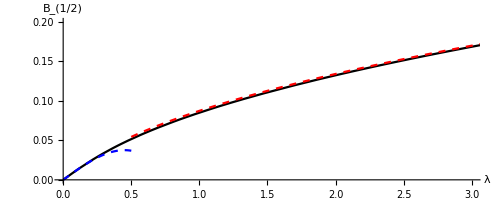

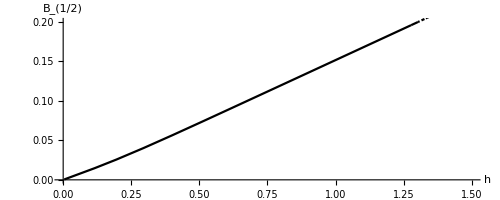

```mathematica
α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

$MaxExtraPrecision=100;


(*Table[{κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16],Re[1/(8π)(ⅈ-(4 ⅈ √(a b)  (1+a b)  EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) π)+(4 ⅈ √a b^(3/2) (3 a+b+a^2 b-a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) (1+a b) π)-(4 ⅈ √(a b) (a+b)EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2])/(π(1+a b )))]},{κ,Table[i,{i,1,1000,20}]}]//N[#,4]&;
ListPlot[%,Joined->True,AxesLabel->{Text[Style["λ",15]],Text[Style["B_(1/2)",15]]},LabelStyle->Directive[FontSize->15],PlotStyle->Black];*)

ParametricPlot[{κ/(8π)HypergeometricPFQ[{1/2,1/2,1/2},{1,3/2},-κ^2/16],Re[1/(8π)(ⅈ-(4 ⅈ √(a b)  (1+a b)  EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) π)+(4 ⅈ √a b^(3/2) (3 a+b+a^2 b-a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) (1+a b) π)-(4 ⅈ √(a b) (a+b)EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2])/(π(1+a b )))]},{κ,0.1,5 10^3},AxesLabel->{Text[Style["λ",20]],Text[Style["B_(1/2)",20]]},LabelStyle->Directive[FontSize->15],PlotStyle->Black,PlotRange->{{0,3},{0,0.2}},AspectRatio->Full];
Plot[λ/8-(π^2 λ^3)/48,{λ,0,0.5},PlotStyle->{Blue,Dashed}];
Plot[(√λ)/(2 √2 π)-1/(4 π^2),{λ,0.5,5},PlotStyle->{Red,Dashed}];
Show[%%%,%%,%]



ParametricPlot[{1/(2π)ArcSinh[κ/4],Re[1/(8π)(ⅈ-(4 ⅈ √(a b)  (1+a b)  EllipticE[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) π)+(4 ⅈ √a b^(3/2) (3 a+b+a^2 b-a b^2) EllipticK[((-1+a^2) (-1+b^2))/(1+a b)^2])/((a-b) (a b-1) (1+a b) π)-(4 ⅈ √(a b) (a+b)EllipticPi[(1-a^2)/(1+a b),((-1+a^2) (-1+b^2))/(1+a b)^2])/(π(1+a b )))]},{κ,0.1,10^4},AxesLabel->{Text[Style["h",20]],Text[Style["B_(1/2)",20]]},LabelStyle->Directive[FontSize->15],PlotStyle->Black,PlotRange->{{0,1.5},{0,0.2}},AspectRatio->Full]



Clear[α,β,a,b]
```

## Generating function g[z]=Sum[V[m]z^m,{m,0,10}]

```mathematica
-(1+2 m)sM V[m]-2 (1+m) (sM tM+tM-3 sM) V[1+m]+(2 m+3) (-tM^2+2 sM tM+2 tM-3 sM) V[2+m]-2 (m+2) (sM-tM) (tM-1)V[m+3]==0;
```

```mathematica
g[z_]:=Sum[V[m] z^m,{m,0,10}]
(g[z]-V[0])/z-Sum[V[m+1] z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal
(g[z]-V[0]-V[1]z)/z^2-Sum[V[m+2] z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal
(g[z]-V[0]-V[1]z-V[2] z^2)/z^3-Sum[V[m+3] z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal

z g'[z]-Sum[V[m]m z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal
g'[z]-(g[z]-V[0])/z-Sum[V[m+1]m z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal
(g'[z]-V[1])/z-2(g[z]-V[0]-V[1]z)/z^2-Sum[V[m+2]m z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal
(g'[z]-V[1] -V[2]2 z)/z^2-3(g[z]-V[0] -V[1] z-V[2] z^2)/z^3-Sum[V[m+3]m z^m,{m,0,10}]//Series[#,{z,0,6}]&//Normal
Clear[g]
```

0

0

0

«4 more identical outputs»

```mathematica
CC[1]==(sM tM+tM-3 sM);
CC[2]==(-tM^2+2 sM tM+2 tM-3 sM);
CC[3]==(sM-tM) (tM-1);
(*/.Flatten[{{V[0]->EllipticK[sM]}, {V[1]->EllipticPi[tM,sM]}, {V[2]->(tM EllipticE[sM]+(sM-tM)EllipticK[sM]+(2 sM tM+2 tM-tM^2-3 sM)EllipticPi[tM,sM])/(2 (sM-tM) (tM-1))}}]
```

```mathematica
-(g[z]+2 (z g'[z]))sM-2 (((g[z]-V[0])/z)+(g'[z]-(g[z]-V[0])/z)) CC[1] +(2 ((g'[z]-V[1])/z-2(g[z]-V[0]-V[1]z)/z^2)+3((g[z]-V[0]-V[1]z)/z^2)) CC[2]-2 (((g'[z]-V[1] -V[2]2 z)/z^2-3(g[z]-V[0] -V[1] z-V[2] z^2)/z^3)+2((g[z]-V[0]-V[1]z-V[2] z^2)/z^3)) CC[3];
%/((2 (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))/z^2)//Collect[#,{g[z],g'[z]},Simplify]&
```

-((sM z^3+z CC[2]-2 CC[3]) g[z])/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))+(z CC[2] V[0]-2 CC[3] V[0]+z^2 (-CC[2] V[1]+2 CC[3] V[2]))/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))-g'[z]

```mathematica
DSolve[{-((sM z^3+z CC[2]-2 CC[3]) g[z])/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))+(z CC[2] V[0]-2 CC[3] V[0]+z^2 (-CC[2] V[1]+2 CC[3] V[2]))/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))-g'[z]==0,g[0]==V[0]},g,z]
```

DSolve::bvnr: For some branches of the general solution, the given boundary conditions do not restrict the existing freedom in the general solution.

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

1.

1.

1.

«3 more identical outputs»

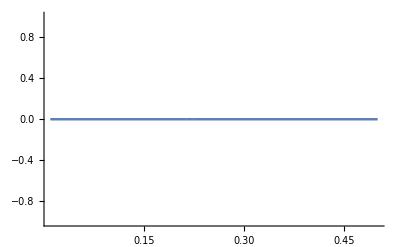

```mathematica
sM=((a^2-1)(b^2-1))/(1+a b)^2;
tM=(1-a^2)/(1+a b);

α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;

VM[n_]:=Switch[n,0,EllipticK[sM],1,EllipticPi[tM,sM],2,(tM EllipticE[sM]+(sM-tM)EllipticK[sM]+(2 sM tM+2 tM-tM^2-3 sM)EllipticPi[tM,sM])/(2 (sM-tM) (tM-1)),_,1/(2 ((n-3)+2) (sM-tM) (tM-1))(-(1+2 (n-3))sM VM[(n-3)]-2 (1+(n-3)) (sM tM+tM-3 sM) VM[1+(n-3)]+(2 (n-3)+3) (-tM^2+2 sM tM+2 tM-3 sM) VM[2+(n-3)])] 

κ=5.2;

CC[1]=(sM tM+tM-3 sM);
CC[2]=(-tM^2+2 sM tM+2 tM-3 sM);
CC[3]=(sM-tM) (tM-1);

Table[r[i]=Root[CC[3]-CC[2] #1+CC[1] #1^2+sM #1^3&,i],{i,3}];

g[z_]:=(ⅈ  z  EllipticE[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (sM z^3+z^2 CC[1]-z CC[2]+CC[3])/(√(z-r[1])) √(r[1]-r[3]) VM[0]+z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √((-r[1]+r[3])/(z-r[1])) VM[0]+ⅈ √(z-r[2]) √(z-r[3]) ((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1])+(ⅈ z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticF[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/(sM √(z-r[1]) √(r[1]-r[3]))-(ⅈ z √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]))/(√sM √(r[1]-r[3])) EllipticF[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √(z-r[2]) √(z-r[3]) (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) √(-z+r[2]) √(z-r[3]))

g[0]/VM[0]//Chop
g'[0]/VM[1]//Chop
g''[0]/(2! VM[2])//Chop
g'''[0]/(3!VM[3])//Chop
g''''[0]/(4!VM[4])//Chop
g'''''[0]/(5!VM[5])//Chop

Plot[{{Re[-((sM z^3+z CC[2]-2 CC[3]) g[z])/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))+(z CC[2] VM[0]-2 CC[3] VM[0]+z^2 (-CC[2] VM[1]+2 CC[3] VM[2]))/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))-g'[z]]//Chop}, {Im[-((sM z^3+z CC[2]-2 CC[3]) g[z])/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))+(z CC[2] VM[0]-2 CC[3] VM[0]+z^2 (-CC[2] VM[1]+2 CC[3] VM[2]))/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))-g'[z]]//Chop}}//Flatten,{z,0.01,0.5}]

Clear[sM,tM, α,β,a,b,VM,κ,CC,r,g,z]
```

```mathematica
F[z_]:=(sM z^3+z CC[2]-2 CC[3])/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))
G[z_]:=(z CC[2] V[0]-2 CC[3] V[0]+z^2 (-CC[2] V[1]+2 CC[3] V[2]))/(2 z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]))
A[z_]:=Log[(√(sM z^3+z^2 CC[1]-z CC[2]+CC[3]))/z]

A'[z]==F[z]//Simplify

Exp[-A[z]](Int[Exp[A[u]]G[u],{u,a,z}]+κ)

Clear[F,G,A]
```

True

(z (κ+Int[(u CC[2] V[0]-2 CC[3] V[0]+u^2 (-CC[2] V[1]+2 CC[3] V[2]))/(2 u^2 √(sM u^3+u^2 CC[1]-u CC[2]+CC[3])),{u,a,z}]))/(√(sM z^3+z^2 CC[1]-z CC[2]+CC[3]))

```mathematica
(ⅈ  z  EllipticE[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (sM z^3+z^2 CC[1]-z CC[2]+CC[3])/(√(z-r[1])) √(r[1]-r[3]) VM[0]+z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √((-r[1]+r[3])/(z-r[1])) VM[0]+ⅈ √(z-r[2]) √(z-r[3]) ((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1])+(ⅈ z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticF[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/(sM √(z-r[1]) √(r[1]-r[3]))-(ⅈ z √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]))/(√sM √(r[1]-r[3])) EllipticF[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √(z-r[2]) √(z-r[3]) (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) √(-z+r[2]) √(z-r[3]));
```

```mathematica
1/((z (1))/(√(sM z^3+z^2 CC[1]-z CC[2]+CC[3])))(ⅈ  z  EllipticE[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (sM z^3+z^2 CC[1]-z CC[2]+CC[3])/(√(z-r[1])) √(r[1]-r[3]) VM[0]+z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √((-r[1]+r[3])/(z-r[1])) VM[0]+ⅈ √(z-r[2]) √(z-r[3]) ((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1])+(ⅈ z (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticF[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/(sM √(z-r[1]) √(r[1]-r[3]))-(ⅈ z √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]))/(√sM √(r[1]-r[3])) EllipticF[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √(z-r[2]) √(z-r[3]) (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) √(-z+r[2]) √(z-r[3]))//Simplify//D[#,z]&;
Collect[%,{EllipticE[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])],EllipticF[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])],EllipticF[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])]},Simplify]
```

(ⅈ EllipticE[ArcSin[√(r[3]/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √(r[1]-r[3]) (2 z CC[1] r[1] r[2] r[3]-CC[2] r[1] r[2] r[3]-2 z CC[3] (r[1]+r[2]+r[3])+CC[3] (r[2] r[3]+r[1] (r[2]+r[3]))-2 z^3 (CC[2]+sM r[2] r[3]+sM r[1] (r[2]+r[3]))+z^4 (CC[1]+sM (r[1]+r[2]+r[3]))+z^2 (3 CC[3]-CC[1] r[1] r[2]-CC[1] r[1] r[3]-CC[1] r[2] r[3]+3 sM r[1] r[2] r[3]+CC[2] (r[1]+r[2]+r[3]))) VM[0])/(2 √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) (z-r[1])^(3/2) (-z+r[2])^(3/2) (z-r[3])^(3/2))+(ⅈ EllipticF[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (2 z CC[1] r[1] r[2] r[3]-CC[2] r[1] r[2] r[3]-2 z CC[3] (r[1]+r[2]+r[3])+CC[3] (r[2] r[3]+r[1] (r[2]+r[3]))-2 z^3 (CC[2]+sM r[2] r[3]+sM r[1] (r[2]+r[3]))+z^4 (CC[1]+sM (r[1]+r[2]+r[3]))+z^2 (3 CC[3]-CC[1] r[1] r[2]-CC[1] r[1] r[3]-CC[1] r[2] r[3]+3 sM r[1] r[2] r[3]+CC[2] (r[1]+r[2]+r[3]))) (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/(2 sM √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) (z-r[1])^(3/2) (-z+r[2])^(3/2) (z-r[3])^(3/2) √(r[1]-r[3]))+(((sM z^3+z^2 CC[1]-z CC[2]+CC[3])^2 EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (z-r[2]) √((-r[1]+r[3])/(z-r[1])) VM[0])/(z-r[3])^(3/2)+((sM z^3+z^2 CC[1]-z CC[2]+CC[3])^2 EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] √((-r[1]+r[3])/(z-r[1])) VM[0])/(√(z-r[3]))+((sM z^3+z^2 CC[1]-z CC[2]+CC[3])^2 EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (z-r[2]) √((-r[1]+r[3])/(z-r[1])) VM[0])/((z-r[1]) √(z-r[3]))+((3 sM z^2+2 z CC[1]-CC[2]) (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) EllipticE[ArcSin[√((-z+r[3])/(-r[2]+r[3]))],(r[2]-r[3])/(r[1]-r[3])] (-z+r[2]) √((-r[1]+r[3])/(z-r[1])) VM[0])/(√(z-r[3]))+((sM z^3+z^2 CC[1]-z CC[2]+CC[3])^2 (z-r[2]) √((-z+r[1])/(r[1]-r[3])) √((-r[1]+r[3])/(z-r[1])) VM[0])/(√(z-r[3]) √(((z-r[2]) (-z+r[3]))/(r[2]-r[3])^2) (-r[2]+r[3]))-(2 ⅈ (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) (z-r[2])^(3/2) ((3 sM z^2+2 z CC[1]-CC[2]) VM[0]+(z (3 sM z^2+2 z CC[1]-CC[2]) √CC[3] VM[1])/(2 √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]))+√CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1]))/z-(ⅈ (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) √(z-r[2]) (sM z^3 VM[0]+z^2 CC[1] VM[0]-z CC[2] VM[0]+CC[3] VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1]))/z+(ⅈ (3 sM z^2+2 z CC[1]-CC[2]) (z-r[2])^(3/2) (sM z^3 VM[0]+z^2 CC[1] VM[0]-z CC[2] VM[0]+CC[3] VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1]))/z+(2 ⅈ (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) (z-r[2])^(3/2) (sM z^3 VM[0]+z^2 CC[1] VM[0]-z CC[2] VM[0]+CC[3] VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1]))/z^2+(ⅈ (sM z^3+z^2 CC[1]-z CC[2]+CC[3]) √(z-r[2]) ((sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[0]+z √CC[3] √(sM z^3+z^2 CC[1]-z CC[2]+CC[3]) VM[1]))/z+(ⅈ (sM z^3+z^2 CC[1]-z CC[2]+CC[3])^2 (z-r[2]) (sM r[1] VM[0]+CC[2] VM[1]-2 CC[3] VM[2]))/(sM √(z-r[1]) √(z-r[3]) √((-z+r[1])/(r[1]-r[3])) √(r[1]-r[3]) √(((z-r[2]) (-z+r[3]))/(r[2]-r[3])^2) (-r[2]+r[3])))/(2 (sM z^3+z^2 CC[1]-z CC[2]+CC[3])^(3/2) (-z+r[2])^(3/2))